```mathematica
ClearAll["Global`*"]
l = 4;
β = 0.5;
snrDB = 8;
ts =1;
snr= 10^(snrDB/20);
var=N[(l^2-1)/(6*Log[2,l]*10^(snrDB/10))];
msum = 20;
ksum = 40;
h[1] := 0;
h[-1] := 0;
h[t_]:=(Sinc[(π t)/ts] Cos[(β π t)/ts])/(1-((2 β t)/ts)^2)
g[k_,Δ_]:=g[k,Δ]=h[(k+Δ) ts]
hermite[n_,y_]:=hermite[n,y]=HermiteH[n,(y/√2)]/2^(n/2)
t[m_]:=t[m] =D[Tan[t],{t,m}]/.t->0
kappa[m_,Δ_]:=N[-(ⅈ^m)*t[m-1]*(l^m-1)/(2^m-1)*Sum[g[-k,Δ]^m + g[k,Δ]^m,{k,1,ksum}]]

alpha[0,Δ_] := 1;
alpha[2,Δ_] := 0;
alpha[4,Δ_] := kappa[4,Δ];
alpha[6,Δ_] := kappa[6,Δ];
alpha[tm_,Δ_]:=alpha[tm,Δ] = kappa[tm,Δ]+Sum[Binomial[tm-1,2*i]*kappa[tm-2*i,Δ]*alpha[2*i,Δ],{i,2,(tm/2)-2}]
sigsqr[Δ_] := sigsqr[Δ]=
N[var + 1/3*(l^2-1)*Sum[g[-k,Δ]^2+g[k,Δ]^2,{k,1,ksum}]] (*sigsqr = σ^2 = variance*)
f[y_,w0_,Δ_] :=N[1/(√(2π*sigsqr[Δ]))*Exp[(-(y-w0*g[0,Δ])^2)/(2*sigsqr[Δ])]*(1+Sum[alpha[2*m,Δ]/((2*m)!*sigsqr[Δ]^(m))*hermite[2*m,(y-w0*g[0,Δ])/(√sigsqr[Δ])],{m,2,msum}])]
```

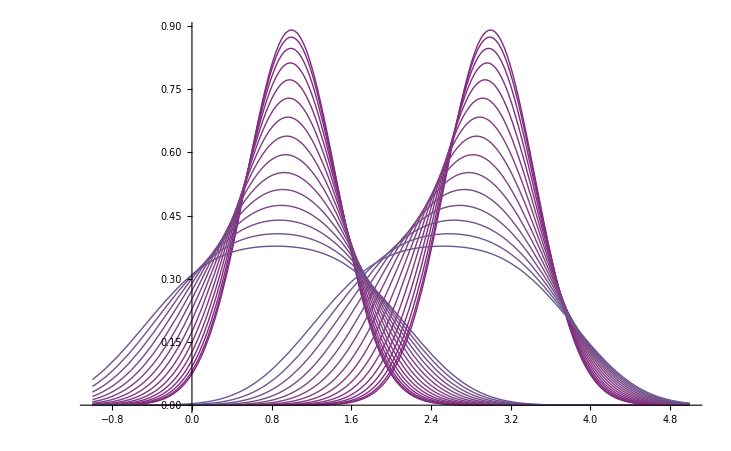

```mathematica
Plot[Evaluate[Join[Table[f[y,1,timing],{timing,0.02,0.3,0.02}],Table[f[y,3,timing],{timing,0.02,0.3,0.02}]]],{y,-1,5},ColorFunction->"Rainbow"]
```

```mathematica
Plotting the difference between P (ω = 1) and P (ω = 3) to visually show the decision region boundaries
```

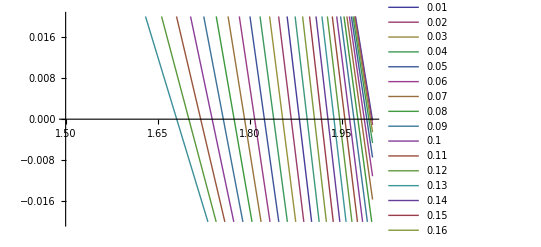

```mathematica
offvals = Range[0.01,0.3,0.01];
dpdf = Monitor[Table[{y,f[y,1,toff]-f[y,3,toff]},{toff,offvals},{y,1.5,2,0.001}],{y,toff}];
ListLinePlot[dpdf,PlotRange->{{1.5,2},{-0.02,0.02}},PlotLegends->offvals]
```

```mathematica
Here I just want to calculate the approximate decision region boundaries, and compare them to 2*g(Δ)
```

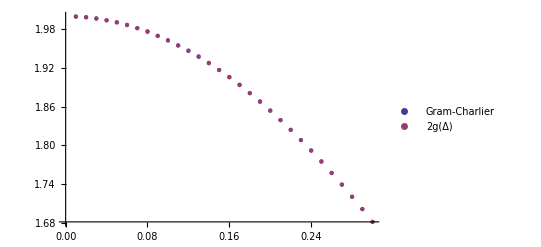

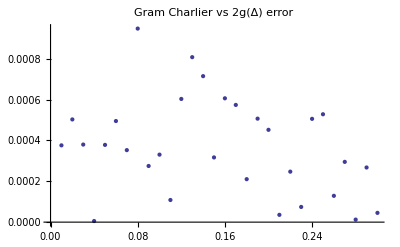

```mathematica
decregbound=1.5+0.001*(Table[Position[dpdf[[toff]],_?(#<0&)][[1,1]],{toff,Length[offvals]}]-1);estimatedrb=Table[2*h[toff],{toff,offvals}];
xydecregbound = Transpose[{offvals,decregbound}];
xyestimatedrb = Transpose[{offvals,estimatedrb}];
MatrixForm[NumberForm[Transpose[{xydecregbound,xyestimatedrb}],{4,3}]];
ListPlot[{xydecregbound,xyestimatedrb},PlotLegends->{"Gram-Charlier","2g(Δ)"}]
ListPlot[Transpose[{offvals,decregbound-estimatedrb}],PlotLabel->"Gram Charlier vs 2g(Δ) error"]
```

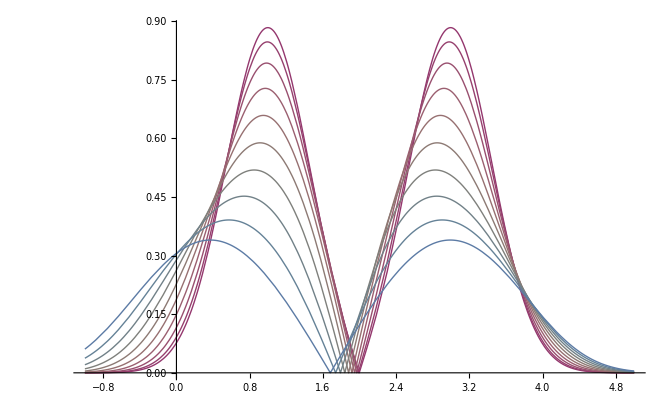

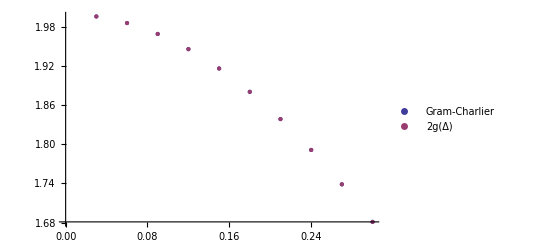

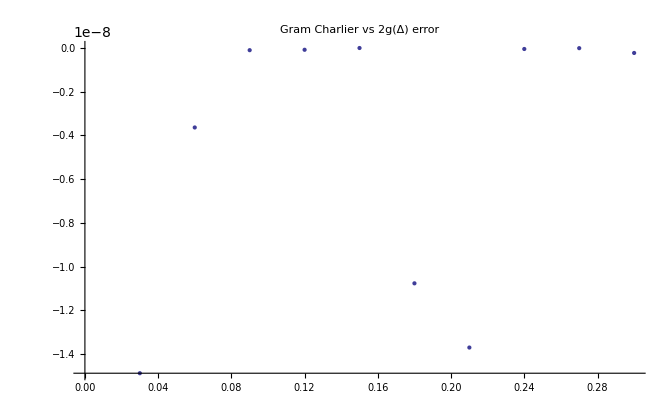

1.4876×10^-8

```mathematica
offvals = Range[0.03,0.3,0.03];
Plot[Table[Abs[f[y,1,o]-f[y,3,o]],{o,offvals}],{y,-1,5},ColorFunction->"Rainbow"]
decregbound = y /.Table[NMinimize[{Abs[f[y,1,o]-f[y,3,o]],y>1.1&&y<2.1},y],{o,offvals}][[All,2]];
estimatedrb=Table[2*h[toff],{toff,offvals}];
xydecregbound = Transpose[{offvals,decregbound}];
xyestimatedrb = Transpose[{offvals,estimatedrb}];
ListPlot[{xydecregbound,xyestimatedrb},PlotLegends->{"Gram-Charlier","2g(Δ)"}]
ListPlot[Transpose[{offvals,decregbound-estimatedrb}],PlotLabel->"Gram Charlier vs 2g(Δ) error"]
Max[estimatedrb-decregbound]
```

{3.29659,2.30044,1.31352,0.648291,0.296365,0.135482}

1.

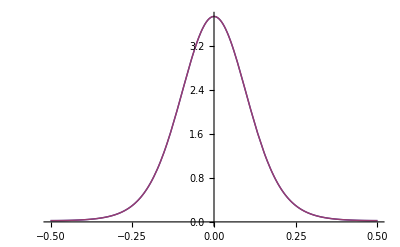

```mathematica
thikfactor[var_]:=thikfactor[var]=1/((2 π)^2 var)
thik[var_,y_]:=thik[var,y]=Exp[thikfactor[var] Cos[2 π y]]/BesselI[0,thikfactor[var]]
NIntegrate[thik[0.01,y],{y,-0.5,0.5}]
thikdist = ProbabilityDistribution[thik[0.01,y],{y,-0.5,0.5}]; (* I don't thinkg ProbabilityDistribution handles cyclic distributions correctly, tbc *)
Plot[{thik[0.01,y],PDF[thikdist,y]},{y,-0.5,0.5}]
```

```mathematica
thiklist=Table[thik[0.01,y],{y,offvals}]
```

```mathematica
thikfactor[var_] := thikfactor[var] = 1/((2*Pi)^2*var);
thik[var_, y_] := thik[var, y] = Exp[thikfactor[var]*Cos[2*Pi*y]]/BesselI[0, thikfactor[var]];
thikdist = ProbabilityDistribution[thik[0.01, y], {y, -0.5, 0.5}]; 
N[RandomVariate[thikdist,{1000}],8]
```

{0.118716,0.0436,0.0910937,-0.045147,-0.071616,-0.00622086,-0.0722244,0.0553735,-0.0744397,0.022472,0.0725963,0.333167,0.0694657,-0.0297963,-0.113069,0.0292027,0.0963751,0.00288972,-0.051045,0.0654554,-0.330334,0.162613,0.193162,-0.0400008,0.0991933,0.0360084,-0.0458254,-0.128208,-0.139634,0.00881442,-0.0446838,0.056045,-0.0678457,0.00781623,-0.0816168,0.0135045,0.101025,-0.066113,-0.105727,-0.141813,0.0513303,-0.0645366,0.146395,-0.043342,-0.142936,-0.278511,0.0021383,-0.114245,0.0968858,0.0195003,-0.0194025,0.0071633,-0.0260286,-0.0570492,0.131513,0.111422,-0.0196721,-0.0586196,0.0658404,0.0197745,0.19063,0.0637503,-0.0330918,0.0444526,-0.0501765,0.0761901,-0.102307,-0.0562022,0.255444,0.210887,0.0621847,-0.029837,-0.0769275,-0.0210096,0.07368,0.0442209,-0.0321977,0.000124711,-0.26644,0.0936417,-0.164505,0.0496152,0.0659082,0.158255,0.164137,-0.0448188,-0.0189048,0.0663052,-0.126202,-0.129505,-0.117078,-0.031481,0.322991,-0.0695643,0.044604,-0.139513,0.12394,-0.0159784,-0.102389,0.0922234,-0.365064,0.0115711,0.0343185,-0.0551587,-0.301161,0.119538,-0.0370765,-0.0118855,0.011282,0.143324,-0.106607,-0.0308777,0.0642778,-0.00235335,-0.134262,0.174787,-0.148257,0.00381451,-0.0640963,-0.115815,0.0749251,0.0306968,-0.00894277,0.0425706,-0.116059,0.0930005,-0.0613054,-0.0136641,-0.0154954,-0.0997549,-0.00938503,0.0175059,0.0558702,-0.0127806,-0.0320754,0.045231,0.0280795,-0.115641,-0.164198,-0.0920439,-0.116621,0.0192123,0.0682625,-0.230532,-0.0849403,0.0510065,0.0393094,0.243727,0.0368727,-0.0612876,0.142577,-0.000380795,0.0526505,0.0631136,0.270329,0.093233,-0.10653,-0.104146,0.0201184,-0.0134985,-0.0884558,0.118016,-0.0130977,0.0570596,0.0384331,0.0258133,0.0270085,-0.133897,0.283915,-0.113804,0.133977,0.0923609,0.075707,-0.0417043,0.0508933,-0.161932,-0.00134432,-0.0493691,-0.0163562,-0.181294,-0.0139349,0.0955745,0.0486104,-0.109978,0.0106866,-0.0722742,-0.162185,0.1512,-0.27961,-0.051008,-0.179177,-0.0530827,-0.235427,-0.0627672,-0.196822,-0.130476,0.151734,0.0703895,0.0347736,-0.157179,0.179165,-0.0615096,-0.178231,-0.0359241,-0.0364755,-0.0148752,0.0752568,-0.0554977,0.0917793,0.0596399,0.0321973,0.0109972,-0.130773,0.0716531,0.157279,0.156688,-0.113194,0.116532,-0.0977803,-0.156063,-0.153806,0.127996,-0.134869,0.0745402,0.282306,-0.0434002,0.126361,0.0242588,-0.0359661,-0.103871,0.0254714,0.0832778,-0.101062,0.121161,0.138394,0.0653449,-0.000408612,0.14423,-0.0976943,0.286101,0.0638323,0.030737,-0.068177,-0.000835692,-0.118557,-0.045776,0.130758,0.0154629,-0.07666,-0.055335,-0.147757,-0.162242,0.100442,-0.0811161,0.0294734,-0.0170885,0.132258,-0.242868,0.125883,0.0173905,-0.00503428,0.0145895,0.026164,0.0399624,-0.035921,-0.0950444,-0.107291,0.062413,0.0503748,0.24775,-0.066722,-0.0350523,0.0731656,0.00952872,0.00563943,-0.041659,-0.0537785,0.00848497,0.0654382,-0.433258,0.0304769,0.0514746,-0.00691092,0.0451531,-0.056003,-0.0588892,0.128567,-0.132073,-0.0590652,0.0044128,-0.0306048,0.0413223,-0.0907816,-0.0140505,-0.121033,-0.071383,-0.337981,-0.0520959,-0.177934,-0.0839195,-0.0623369,-0.0851632,0.0901315,0.109626,-0.032536,0.00453644,-0.138988,-0.150094,0.0991309,0.066359,0.0563415,0.0184938,0.0223836,-0.0238987,0.0354788,0.0215765,0.125819,-0.00863742,0.0358284,-0.0793636,-0.104985,0.123264,0.0120578,0.0804619,0.0466799,-0.220334,0.0447951,-0.103318,0.0677221,0.0928514,0.0432812,-0.028112,0.0343902,-0.109373,0.102381,0.0861458,-0.0253475,-0.0113836,-0.010532,0.0908662,0.157155,0.0574341,0.108633,0.191528,0.156488,-0.19445,0.0110699,0.0425,-0.0468643,-0.158426,-0.0966067,-0.00523561,0.0241294,-0.167791,-0.181605,0.0480747,-0.0564871,0.0398,-0.0968074,-0.00929457,-0.0704362,-0.0663304,0.0897587,-0.0301182,-0.206153,0.135601,0.192403,0.0214814,0.0511066,-0.0909156,0.226451,0.0805808,-0.0414656,0.0586436,-0.2244,-0.0583114,-0.0917865,0.200894,0.0429362,-0.100151,-0.115934,0.0329893,0.171651,0.158775,-0.156362,-0.119665,-0.225998,-0.0724222,-0.00500083,-0.020714,-0.0842246,-0.117807,-0.480229,-0.0165298,0.100252,0.16028,-0.116581,-0.0514082,0.0825904,-0.362646,-0.0864835,-0.0349696,-0.047577,0.289494,0.0682433,-0.0818777,-0.131408,0.0849194,-0.0693602,-0.155778,-0.245016,0.175274,-0.0388834,0.0335083,-0.205923,0.0655938,-0.0549654,-0.0337935,-0.0383002,0.319891,0.0668151,0.00208285,0.0833074,0.0138344,0.169918,0.0286749,-0.0149193,-0.11758,0.0965188,0.00992154,-0.0851382,-0.0115734,-0.0629965,-0.164123,-0.0551042,0.00594967,-0.0117777,-0.0142144,-0.0850812,-0.02218,-0.018855,-0.0251185,-0.0192267,-0.0796759,-0.101151,-0.0846321,0.0166928,-0.097368,0.0316335,0.141034,0.0342636,-0.120298,0.022065,-0.142984,0.098215,-0.111048,0.0844513,-0.116771,-0.136286,0.126131,-0.155107,-0.0577588,0.270947,0.106905,-0.229007,-0.19104,-0.139447,-0.294714,0.0136762,0.0842985,-0.188332,-0.0222446,0.160522,0.222044,0.0499257,-0.0512916,0.224191,-0.030023,-0.150676,-0.126465,-0.0620883,-0.0569968,-0.0802535,0.0357644,-0.0848813,0.0427634,-0.303567,-0.0264678,0.0199099,0.00398474,0.0873937,0.19466,-0.0151742,-0.0897409,-0.0347982,-0.268928,-0.0860699,-0.108691,-0.0623557,0.0457366,0.0776098,0.0628475,-0.0547922,0.00569883,0.169941,-0.00159547,-0.033685,0.0883672,0.100725,-0.123357,0.000458427,-0.00845216,0.0501152,-0.160525,0.136419,-0.189994,0.0074861,-0.100336,0.0403839,-0.0875706,0.0401704,-0.120384,-0.280582,-0.215887,-0.0811331,0.1586,-0.0446185,0.00206293,0.0240189,-0.0889104,0.062356,0.12541,0.0923272,-0.0162206,0.00635895,0.0754773,0.0668108,0.10221,0.150248,-0.0630366,-0.0337355,0.098707,0.034661,0.0620573,0.252054,-0.231536,-0.0294418,0.215868,0.00668953,0.0553303,0.00207279,-0.183651,-0.0893482,-0.182298,0.214991,-0.0732566,0.0735335,0.0725469,-0.140419,-0.0499624,-0.0214059,0.00853617,-0.141633,-0.0493513,0.0198159,-0.0300248,-0.027256,-0.0489693,0.0949313,-0.0299791,-0.0181428,-0.199139,-0.0378433,0.0665547,0.0308665,-0.0442703,-0.103525,0.071603,0.0703799,-0.0252274,0.132076,-0.0577712,-0.0785925,0.280081,0.075165,0.136677,-0.071836,0.107478,0.136703,0.139668,-0.103683,-0.0261672,-0.127673,-0.036675,-0.0900787,-0.199691,-0.0665398,-0.0964107,0.0722082,-0.215432,-0.152742,0.045131,-0.00442172,0.282342,-0.0701068,-0.0879298,0.0996143,-0.073569,-0.0195542,0.0388997,-0.130877,-0.113502,0.11513,0.233783,0.0992029,0.0132502,-0.0315569,0.157475,0.028916,0.0803758,-0.0271567,-0.0855195,-0.0274421,0.0167789,0.101379,0.0746322,-0.0819775,0.016697,-0.0633812,-0.11218,0.0330096,0.250538,0.0439987,0.00878863,-0.0327795,0.0810379,-0.124535,0.0710447,-0.0449946,0.104058,-0.0647033,0.145826,-0.0408367,-0.0016713,-0.0407289,0.278438,-0.0269205,-0.0522958,-0.33977,0.0652171,-0.0324699,-0.101197,-0.132083,0.0114748,-0.118266,0.221161,-0.222347,0.0108847,0.0662903,0.000107724,0.194942,0.110416,0.0829472,0.0545948,-0.149044,0.125528,0.330743,-0.0328904,0.212891,0.18397,-0.128376,-0.120702,-0.0955857,-0.0598427,-0.0367166,0.135469,-0.0192688,-0.0664992,0.0441576,0.209787,-0.0712209,-0.0586607,0.0378393,0.0321863,-0.0733486,0.00507102,0.132565,-0.0902301,-0.115112,0.126144,-0.218662,0.0163612,0.00266402,0.376237,0.0657784,-0.121708,-0.109085,0.0911362,0.0451163,-0.0468896,0.059775,0.0257919,-0.0814205,-0.159694,-0.0430931,-0.0296884,-0.0125222,-0.111017,0.0421576,0.222927,0.212924,-0.0490656,0.115462,0.046063,-0.245459,-0.155767,-0.00655204,0.174775,-0.142453,0.220562,-0.163739,0.0486459,0.0730527,0.0155478,0.0861246,-0.0398716,0.079915,-0.00919326,-0.0713884,0.0321845,-0.106466,0.042611,-0.0083255,0.124817,0.0636388,-0.0109545,-0.0143568,0.0970516,-0.0345951,0.041931,-0.025617,0.0465743,0.133258,-0.0314782,-0.0632953,0.00787493,0.135449,-0.158694,-0.0401156,0.0275027,0.16863,0.0829051,-0.19114,-0.173791,-0.00723431,0.0168135,0.00818982,-0.11248,0.0628752,-0.12853,0.0123105,0.000331092,0.00951433,0.0696574,-0.033499,-0.114026,0.189642,0.105158,0.12313,0.0344899,-0.243721,-0.0286043,0.0428771,-0.128541,-0.0543088,-0.0589512,-0.00999561,0.126441,-0.152404,0.00144595,0.193532,-0.0349143,0.171449,0.169528,0.123536,-0.106012,0.0638413,0.0855408,-0.160683,-0.0163194,-0.0860865,-0.149654,0.104002,0.0562203,0.062769,0.0437446,-0.0266714,-0.130587,-0.169424,0.159249,0.109293,-0.0542984,0.0251458,-0.0264386,-0.0374983,0.066448,-0.0442893,0.0739637,0.045523,0.0613088,-0.033269,0.097965,-0.0158879,0.239098,-0.0826344,-0.181527,-0.108515,0.0616011,-0.076153,-0.114015,0.0981609,-0.0114948,0.124466,0.0162988,0.0150678,0.271206,-0.125973,-0.0985599,-0.137777,-0.2388,0.031728,0.148359,-0.0128893,0.099845,-0.008174,0.0137565,0.0339763,0.0833224,0.0207207,0.275458,-0.0111978,-0.142383,-0.00962935,-0.194074,-0.440184,0.0987938,-0.0966582,-0.110037,0.00495572,-0.0127877,0.147864,0.063286,-0.072791,0.0719498,-0.0989575,0.0545088,0.144888,0.0142127,0.106921,0.0976931,-0.114525,0.187742,0.0360671,0.00862238,0.00496088,-0.147394,-0.457036,0.0952335,-0.0234417,-0.0203962,0.199518,-0.0328846,0.153204,0.0945658,-0.0223929,0.0245165,0.164767,0.0806512,0.0177958,-0.01756,0.0507102,-0.0671208,-0.0868921,0.146883,0.0194912,-0.21695,0.0566359,-0.102855,-0.0289225,-0.0705403,0.259322,0.00522093,0.105947,-0.111335,0.00574994,0.0219789,0.124781,-0.023572,0.0951418,-0.0806878,-0.101361,-0.117144,0.11726,-0.061382,-0.0202165,-0.0176811,0.116557,0.000548168,0.00143076,0.0873071,-0.141889,-0.251985,0.0387307,-0.0827328,-0.0727139,-0.137842,-0.0420456,-0.186052,0.151147,-0.0678093,-0.169544,-0.0997241,0.109952,0.156036,-0.0993669,-0.263389,0.0967704,-0.0532785,0.0877703,-0.0440713,0.0493215,0.167419,0.15072,-0.0482686,-0.0543058,-0.154787,-0.255328,-0.098477,0.065648,0.0386651,-0.0372039,-0.0618054,0.0107291,0.189692,-0.0183817,-0.170314,-0.11423,0.0616684,-0.187342,0.0280793,-0.0546934,-0.0285699,-0.0382502,-0.0101921,-0.206954,0.0376961,0.0692813,-0.00378662,0.0917927,-0.0140457,0.265257,-0.0723355,0.0508906,-0.0887161,0.0347527,0.0979869,-0.152963,0.00551455,-0.0309311,0.292879,0.083817,0.0596346,0.139019,-0.140899,-0.0120588,0.0194876,0.0119872,-0.0816736,0.0126767,-0.096151,-0.000827345,-0.168766,0.0664887,-0.168202,-0.156274,-0.214377,-0.181316,-0.0487223,0.0820281,0.00459627,-0.00885472,-0.1173,-0.040675,-0.0912239,0.154354,-0.167502,-0.0298525,0.0410357,0.0829322,-0.00691765}

```mathematica
y /.decregbound[[All,2]]
```

{1.99662,1.98651,1.96973,1.9464,1.91668,1.88079,1.83896,1.79149,1.73871,1.68095}